```mathematica
Clear[α,β]
```

```mathematica
Solve[Integrate[PDF[NormalDistribution[-1,1.5],x],{x,α,100}]==0.95,α]
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{{α→-3.46728}}

```mathematica
fFindAlpha[β_]:=NSolve[Integrate[PDF[NormalDistribution[-1,1.5],x],{x,α,β}]==0.95,α,Reals][[1,1,2]]
```

```mathematica
fFindAlpha[10]
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

-3.46728

```mathematica
fFindBeta[α_]:=NSolve[Integrate[PDF[NormalDistribution[-1,1.5],x],{x,α,β}]==0.95,β,Reals][[1,1,2]]
```

```mathematica
fFindBeta[-100]
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

1.46728

```mathematica
fFindAlphaSymmetric:=NSolve[Integrate[PDF[NormalDistribution[-1,1.5],x],{x,-1-α,-1+α}]==0.95,α,Reals][[1,1,2]]
```

```mathematica
fFindAlphaSymmetric
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

2.93995

```mathematica
Clear[g1]
```

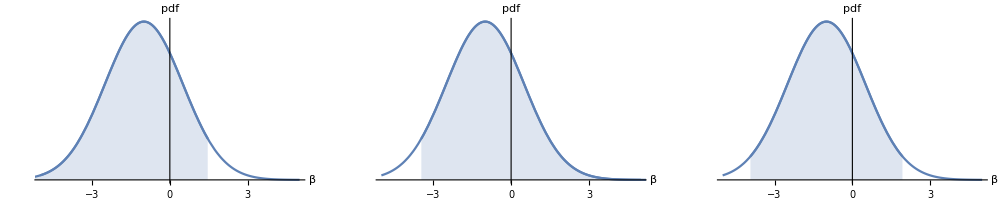

```mathematica
g1=Show[Plot[PDF[NormalDistribution[-1,1.5],x],{x,-5,5},AxesLabel->{"β","pdf"},BaseStyle->{FontSize->16},PlotRange->Full,Ticks->{Automatic,None}],Plot[PDF[NormalDistribution[-1,1.5],x],{x,-10,1.46},Filling->Axis,PlotRange->{Automatic,{0,0.35}}]];
g2 = Show[Plot[PDF[NormalDistribution[-1,1.5],x],{x,-5,5},AxesLabel->{"β","pdf"},BaseStyle->{FontSize->16},PlotRange->Full,Ticks->{Automatic,None}],Plot[PDF[NormalDistribution[-1,1.5],x],{x,-3.46,10},Filling->Axis,PlotRange->{Automatic,{0,0.35}}]];
g3 = Show[Plot[PDF[NormalDistribution[-1,1.5],x],{x,-5,5},AxesLabel->{"β","pdf"},BaseStyle->{FontSize->16},PlotRange->Full,Ticks->{Automatic,None}],Plot[PDF[NormalDistribution[-1,1.5],x],{x,-1-2.93,-1+2.93},Filling->Axis,PlotRange->{Automatic,{0,0.35}}]];
Show[GraphicsRow[{g1,g2,g3}],ImageSize->1000]
```